# GNU Scientific Library (GSL)

```mathematica
PacletDirectoryLoad["~/GSLLink"];
```

```mathematica
Get["WolframExternalFunctions`GSLLink`"];
```

#### checks

```mathematica
$ContextAliases["gsl`"]="WolframExternalFunctions`GSLLink`Private`"
```

WolframExternalFunctions`GSLLink`Private`

```mathematica
Block[{$Context="WolframExternalFunctions`GSLLink`Private`"},
Names["gsl`gsl*"]
]
```

#### AiryAi

```mathematica
(* second arg '0' is double precision *)
Comap[{AiryAi,gsl`gsl˘sf˘airy˘Ai[#,0]&},2.3]
```

{0.021832,0.021832}

```mathematica
Comap[{AiryAiPrime,gsl`gsl˘sf˘airy˘Ai˘deriv[#,0]&},2.3]
```

{-0.0351731,-0.0351731}

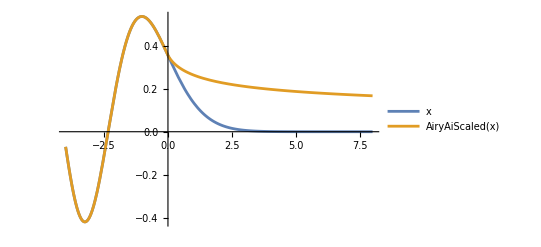

```mathematica
Plot[{AiryAi[x],AiryAiScaled[x]},{x,-4,8},PlotLegends->"Expressions"]
```

```mathematica
(* we don't have a 'scaled' version in System` *)
```

```mathematica
AiryAiPrimeScaled[2.3]
```

-0.359854

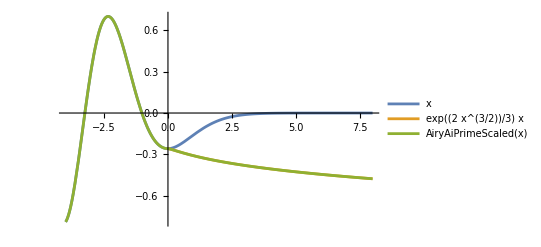

```mathematica
Plot[{AiryAiPrime[x],Exp[(2/3)*x^(3/2)]AiryAiPrime[x],AiryAiPrimeScaled[x]},{x,-4,8},PlotLegends->"Expressions"]
```

#### AiryBi

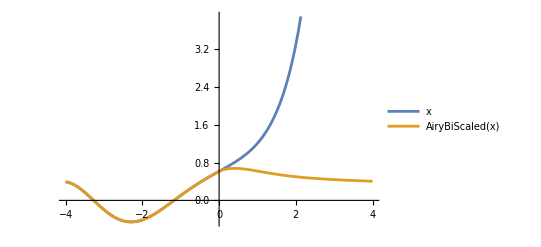

```mathematica
Plot[{AiryBi[x],AiryBiScaled[x]},{x,-4,4},PlotLegends->"Expressions"]
```

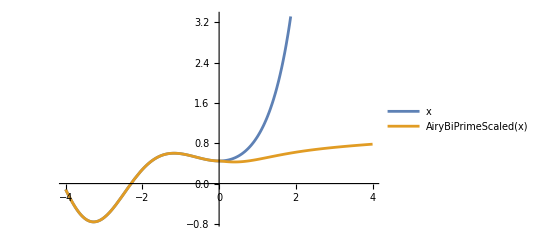

```mathematica
Plot[{AiryBiPrime[x],AiryBiPrimeScaled[x]},{x,-4,4},PlotLegends->"Expressions"]
```

#### AiryAiPrimeZero

```mathematica
AiryAiPrimeZero[4]
```

-6.16331

```mathematica
FindRoot[AiryAiPrime[x],{x,-6.0}]
```

{x→-6.16331}

#### checks

```mathematica
Comap[{Zeta,gsl`gsl˘sf˘zeta},2.3]
```

{1.43242,1.43242}

```mathematica
Comap[{Gamma,gsl`gsl˘sf˘gamma},2.3]
```

{1.16671,1.16671}

```mathematica
?gsl`gsl˘sf˘lnsinh
```

```mathematica
Do[gsl`gsl˘sf˘lnsinh[2.3],1000]//AbsoluteTiming
```

{0.012607,Null}

```mathematica
Do[Log[Sinh[2.3]],1000]//AbsoluteTiming
```

{0.000728,Null}

## Older

```mathematica
gslComplexAbs[{3,4}]
```

5.

```mathematica
gslComplexAbs2[{3,4}]
```

25.

```mathematica
gslComplexAdd[{2,3},{5,7}]
```

{7.,10.}

```mathematica
gslComplexAddImag[{2,3},3]
```

{2.,6.}

```mathematica
gslComplexAddReal[{2,3},3]
```

{5.,3.}

```mathematica
gslComplexArg[{3,4}]
```

0.927295

```mathematica
gslComplexConjugate[{3,4}]
```

{3.,-4.}

```mathematica
gslComplexDiv[{2,3},{5,7}]
```

{0.418919,0.0135135}

#### matrices

Allocate memory for a matrix:

```mathematica
ptr=gslMatrixAlloc[4,4]
```

RawPointer[…]

Define a sample matrix:

```mathematica
mat={{7,0,0,0},{0,5,0,0},{0,0,3,0},{0,0,0,2}};
```

Compute the eigen-values:

```mathematica
Eigenvalues[mat]
```

{7,5,3,2}

Set the values one at a time:

```mathematica
Do[gslMatrixSet[ptr,i,j,mat[[i+1,j+1]]],{i,0,3},{j,0,3}]
```

Check that the values were correctly set:

```mathematica
Table[gslMatrixGet[ptr,i,j],{i,0,3},{j,0,3}]
```

{{7.,0.,0.,0.},{0.,5.,0.,0.},{0.,0.,3.,0.},{0.,0.,0.,2.}}

Try to use the matrix in a Cholesky decomposition. It crashes (?):

```mathematica
gslLinalgCholeskyDecomp1[ptr]
```

gslLinalgCholeskyDecomp1[RawPointer[…]]

### Special Functions

#### gslAiryAi

```mathematica
Quit
```

```mathematica
gslAiryAi[1.2]
```

ForeignFunction::argtype: Expected an argument with type RawPointer::[ListTuple::[CDouble,CDouble]] but found RawPointer[…] instead.

If[$Failed≠0,Message[gslAiryAi::error,WolframExternalFunctions`GSLLink`Private`status],WolframExternalFunctions`GSLLink`Private`result$11743]

```mathematica
ptr=RawMemoryAllocate[TypeSpecifier["ListTuple"]["CDouble","CDouble"]]
```

ManagedObject[…]

```mathematica
WolframExternalFunctions`GSLLink`Private`airyai//InputForm
```

ForeignFunction["/Users/arnoudb/GSLLink/Kernel/Libraries/MacOSX-ARM64/libgsl.27.dylib", 
 "gsl_sf_airy_Ai_e", DataStructure["RawForeignFunction", 
  {"FunctionPointer" -> OpaqueRawPointer[4920947348], 
   "Type" -> {"CDouble", "CUnsignedInt", TypeSpecifier["RawPointer"][TypeSpecifier["ListTuple"][
        "CDouble", "CDouble"]]} -> "CInt"}]]

```mathematica
ptr=RawMemoryAllocate@OpaqueRawPointer[0]
```

ForeignFunction::invtype: OpaqueRawPointer[…] cannot be used as a foreign function interface type.

$Failed

```mathematica
WolframExternalFunctions`GSLLink`Private`airyai[1.2,0,ptr]
```

0

https://www.gnu.org/software/gsl/doc/html/specfunc.html#clausen-functions

```mathematica
Clausen[1.2]
```

1.00539

```mathematica
list=Table[Clausen[x],{x,0.0,40.0,0.1}];
```

```mathematica
ListLinePlot[list]
```

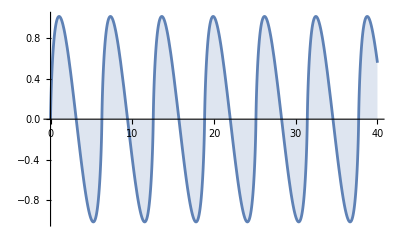
{0.041753,-Graphics-}

```mathematica
Plot[Clausen[x],{x,0.0,40.0},Filling->Axis,PlotHighlighting->None] //AbsoluteTiming
```

```mathematica
Plot[ResourceFunction["ClausenCl"][2,x],{x,0.0,40.0},Filling->Axis,PlotHighlighting->None] //AbsoluteTiming
```

{0.578327,-Graphics-}

```mathematica
Do[Clausen[RandomReal[]],10000]//AbsoluteTiming
```

{0.078447,Null}

```mathematica
Do[ResourceFunction["ClausenCl"][2,RandomReal[]],10000]//AbsoluteTiming
```

{3.12823,Null}

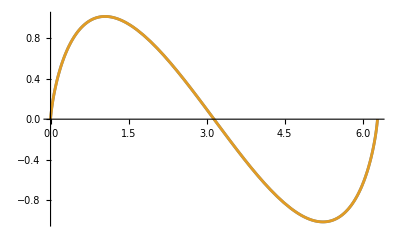

```mathematica
Plot[{Clausen[θ],ResourceFunction["ClausenCl"][2,θ]},{θ,0,2 π}]
```